## Generate blocks (Set Directories here)

```mathematica
prec=vhprec = 600;
nprec=2048;
one=1//SetPrecision[#,prec]&;
rho = SetPrecision[3-2 Sqrt[2], prec];
bldirectory = "/home/workdirectory/blocks2d/";
scalarblock="/home/scalar_blocks/build/scalar_blocks";
sdpdirectory="/home/ising2ddata/";
pvmcommand="mpirun --allow-run-as-root -n 6 ~/MEGA/libraries/sdpb/build/pvm2sdp 2048 ";
sdpbcommand="mpirun --allow-run-as-root -n 6 ~/MEGA/libraries/sdpb/build/sdpb";
<<"/home/nima/MEGA/UChicagoWork/nl-bootstrap/check files/SDPB.m";
```

## Block Settings

```mathematica
d=2+10^-9;
myΔ12 = 0; myΔ34 = 0;
myNmax=4;
myKPO = 10;
recursionOrder = 40;
spins=Table[L,{L,0,14,2}];
 derivs = Select[Flatten[Table[Table[{Np, Nm}, {Np, Nm,2myNmax,1}], {Nm, 0, 2myNmax, 1}],1], Plus@@#≤2 myNmax-1&]//Sort;
oddD=derivs/.{a_,b_}/;EvenQ[a+b]->Nothing
evenD=derivs/.{a_,b_}/;OddQ[a+b]->Nothing;
oddD=oddD[[1;;8]];
```

{{1,0},{2,1},{3,0},{3,2},{4,1},{4,3},{5,0},{5,2},{6,1},{7,0}}

```mathematica
dersij2=Binomial[i,K[1]] FactorialPower[Δϕ,K[1]] (-1)^(1-K[1]-K[2]-K[3]) 2^(-2 Δϕ 0+K[1]+K[2]+K[3]) ((-1)^(1+i+j)+1) zzbDeriv[i-K[1],j-K[2]-K[3]] FactorialPower[Δϕ-K[1],K[3]] FactorialPower[K[1],K[2]] Multinomial[K[2],j-K[2]-K[3],K[3]]K[2]0jK[3]0jK[1]0i;
zzbDerivTablePath2[tableDir_,d_,delta12_,delta34_,L_,nmax_,keptPoleOrder_,order_]:=tableDir<>"/zzbDerivTable-d"<>ToString[d//SetPrecision[#,10]&]<>"-delta12-"<>ToString[delta12]<>"-delta34-"<>ToString[delta34]<>"-L"<>ToString[L]<>"-nmax"<>ToString[nmax]<>"-keptPoleOrder"<>ToString[keptPoleOrder]<>"-order"<>ToString[order]<>".m"
isingfile2[d_,L_, KPO_] := zzbDerivTablePath2[bldirectory, d,SetPrecision[myΔ12,prec],SetPrecision[myΔ34,prec], L, myNmax, KPO, recursionOrder];
polys1[d_]:=polys1[d]=Module[{},
If[!(And@@Table[FileExistsQ[isingfile2[d,L,myKPO]], {L, spins}]),Print["making files"];
Run[scalarblock<>" --output-poles --dim "<>ToString[d//SetPrecision[#,10]&]<>" --order "<>ToString[recursionOrder]<>" --max-derivs "<>ToString[myNmax]<>" --spin-ranges "<>StringReplace[StringTake[ToString[spins],{2,-2}]," "->""]<>" --poles  "<>ToString[myKPO]<>" --delta-12  "<>ToString[myΔ12]<>" --delta-34  "<>ToString[myΔ34]<>" --precision  "<>ToString[nprec]<>"  --num-threads 6 -o "<>bldirectory]
];
 (Table[Import[isingfile2[d,L,myKPO]], {L, spins}]//Expand)//Chop[#,10^-100]&
]

poles[d_,L_]:=Module[{sh},
sh=(shiftedPoles/.(polys1[d]⟦Position[spins,L]//First//First⟧//Last//Rationalize));
(*Print[sh];*)
If[Length@sh==2,Join[sh[[1]],sh[[2]],sh[[2]]],sh//Flatten]
]
Qpoles[d_,s_]:=Module[{pl=poles[d,s]},
(x-(pl)/.List->Times)^-1(4rho)^(x+s+(d-2))
]
bpoly[d_,ii_,jj_,z_,L_]:=Chop[-If[EvenQ[ii+jj+1],(((dersij2/.{i->ii,j->jj}//Activate)/.{zzbDeriv[a_,b_]/;a<b->zzbDeriv[b,a]}/.polys1[d]⟦Position[spins,L]//First//First⟧)),0] //Expand//Quiet,10^-300]/.x->z
```

## SDPB

## bisection

```mathematica
Clear[Δϕ,ΔGap,vac]
runsingle[d1_,d2_,dim_]:=Module[{myy,Δϕ1,ΔGap,pols,pols2,norm,obj,identity,sdpFile,sdpFolder,outFile,vac,fullResult,terminateReason},
Δϕ1=d1//SetPrecision[#,prec]&;
ΔGap=d2//SetPrecision[#,prec]&;
vac=-Table[(-1)^(1-i-j) 2^(i+j) (1+(-1)^(1+i+j)) FactorialPower[Δϕ,i] FactorialPower[Δϕ,j]/.{i->vindex[[1]],j->vindex[[2]]} ,{vindex,oddD}]/.Δϕ->Δϕ1//FunctionExpand//Expand;
pols=
Table[
PositiveMatrixWithPrefactor[
(*DampedRational[1,{},rho,x]*)DampedRational[1,poles[dim,Li],rho,x]If[Li==0,1,x],
{
{
Table[Chop[(*If[Li==0,1,1/x]*)If[Li==0,1,1/x]bpoly[dim,vindex[[1]],vindex[[2]],x,Li]/.Δϕ->Δϕ1/.x->x+If[Li==0,-(dim-2)+ΔGap,0]//Expand,10^-300],{vindex,oddD}]
}
}
],
{Li,spins}];
identity=PositiveMatrixWithPrefactor[
DampedRational[1,{},rho,x],
{
{
vac
}
}
];
obj=0vac;
norm=vac;
pols2=pols;
sdpFile = sdpdirectory<>"isingbs.xml";
sdpFolder = sdpdirectory<>"isingbs";
outFile = sdpFolder<>"_out/out.txt";
Close[sdpFile]//Quiet;
WriteBootstrapSDP[sdpFile,SDP[obj,norm,pols2]];

Run[pvmcommand<>sdpFile<>" "<>sdpFolder];
Run[sdpbcommand<>" --precision=2048 --procsPerNode=2","-s",sdpFolder," --findDualFeasible --findPrimalFeasible --stepLengthReduction=0.7  --dualityGapThreshold=1e-30 --primalErrorThreshold=1e-30 --dualErrorThreshold=1e-30 --maxIterations=300   --initialMatrixScalePrimal=1e30 --initialMatrixScaleDual=1e30 --feasibleCenteringParameter=0.1 --infeasibleCenteringParameter=0.3 --maxComplementarity=1e100"];
fullResult = Import[outFile, "String"];
 terminateReason = StringCases[fullResult,"terminateReason = \""~~Shortest[a__]~~"\";\n" :> a][[1]];
    Switch[
        terminateReason,
        "found primal feasible solution", True,
        "found dual feasible solution", False,
        _, Throw[terminateReason]]
]
msg="";
binarySearch[f_, true_, false_, thresh_,prev_] := Module[
    {test = (true + false)/2,rest},
    If[Abs[true - false] < thresh∧!prev,
       false,
       (*WriteString["stdout", "> trying: ", test, "\n"];*)
msg=" trying: "<> ToString[test];
       rest=f[test];
If[rest,
          binarySearch[f, test, false, thresh,rest],
          binarySearch[f, true, test,  thresh,rest]]]];
```

```mathematica
initdf=145*10^-3;
Print@Dynamic@msg
tmpgap=binarySearch[
             runsingle[initdf, #,2+10^-9] &, 
           1//SetPrecision[#,prec]&,
         1.2//SetPrecision[#,prec]&,
             10^-4,False]
```

1.079980468749999982240768414687437370957923121750354766845703125

## Optimization

```mathematica
optsdp[d1_,d2_?NumericQ,dim_]:=Module[{myy,ΔGap=d2//SetPrecision[#,prec]&,pols,pols2,norm,obj,identity,sdpFile,sdpFolder,outFile,vac},
vac=-Table[(-1)^(1-i-j) 2^(i+j) (1+(-1)^(1+i+j)) FactorialPower[Δϕ,i] FactorialPower[Δϕ,j]/.{i->vindex[[1]],j->vindex[[2]]} ,{vindex,oddD}]/.Δϕ->d1//SetPrecision[#,prec]&//FunctionExpand//Expand;
pols=
Table[
PositiveMatrixWithPrefactor[
DampedRational[1,poles[dim,Li],rho,x]If[Li==0,1,x],
{
{
Table[Chop[If[Li==0,1,1/x]bpoly[dim,vindex[[1]],vindex[[2]],x,Li]/.Δϕ->d1/.x->x+If[Li==0,-(dim-2)+ΔGap,0]//SetPrecision[#,prec]&//Expand,10^-300],{vindex,oddD}]
}
}
],
{Li,spins}];
norm=Table[KroneckerDelta[i-1],{i,oddD//Length}];
obj=vac;
norm=Table[1,{i,obj//Length}];
pols2=pols;
sdpFile = sdpdirectory<>"isingopt.xml";
sdpFolder = sdpdirectory<>"isingopt";
outFile = sdpFolder<>"_out/out.txt";
Close[sdpFile]//Quiet;
WriteBootstrapSDP[sdpFile,SDP[obj,norm,pols2]];
Run[pvmcommand<>sdpFile<>" "<>sdpFolder];
Run["kitty --hold "<> sdpbcommand<>" --precision=2048 --procsPerNode=6","-s",sdpFolder,"  --stepLengthReduction=0.7  --dualityGapThreshold=1e-30 --primalErrorThreshold=1e-30 --dualErrorThreshold=1e-30 --maxIterations=300   --initialMatrixScalePrimal=1e30 --initialMatrixScaleDual=1e30 --feasibleCenteringParameter=0.1 --infeasibleCenteringParameter=0.3 --maxComplementarity=1e100 --noFinalCheckpoint"];
 myy=(Import[sdpFolder<>"_out/y.txt","Data"]//ToExpression)/.{a_+b_ e:>b 10^a};
myy[[1]]=a;
myy[[1]]=a/.Solve[( myy ).(norm )==1]//First;
Print[myy.obj//N];
myy
]
```

```mathematica
inityy=optsdp[initdf,tmpgap,2+10^-9]
```

## Load data with running SDPB (run if don’t have SDPB installed)

```mathematica
inityy={0.085046374019039736759779362679524058946527803635183868461113771674980366866945713847325018870516273458083034194866956280950841375091106403476425944019101743500210200527656573613727045700169182646439199310014545748285611788555383812041910706034597974462002861820406913426993074588895715282878431220791578577834863325647529181695324777815903539650843188608672678981600224299444046394008146697213160871860754786727849083713720994065697179644489023785652396150195076899701775834217820712724474895154442331805995827702903206760358800464813602952091118814812765817421791813928922004713525037684414970265960476142600178450705035999999999999999`614.8796590744307,1.034653403588458942548355846704619640355780764438034707287176961574060808696736707634211397820919147789949957889284866344302471712959129968729827199729890869081443176985359162772584097335517148779415344523211537459947124331483962575114622480661671591307155698505711063794984316581210020363352938632838065897888708473964105777443270088527581815336588896208626486795248481194531752112134793357078357282728884413478921498196345966094646470995212557598604227257144881984160983010052523748578243508323718201281254365516130153736316846831092075850814145021254236339976410851580135028836934853368601051545002773284423151781699999999999999999999`616.0147948907415,0.015613846222700940763754729561958373425093459302867084939467458615409407352500181436103838580382583839131261327824153489638674337236723087910225569738076668256490405616044342944895732181516588011945885823275261165908449101634058020292794079995206851693731056905455296687391990727467404039369909845564971112282015962036183636030517549434408888839605121161714992121197257947504036627545548454988841429099862072302626364045703514900365039668489543217693872649989072058473279059558368279187249228322656461875197216056831700185596800482781160751735320896056488133784804164292321066558874142874200997295804273824216217738891`616.19350989778,-0.12561887065112530763463187820596390163481567427236730333129152380383009264929560442704105261898212409467128584676538273229325141367153407659256975008177466137548590606816013887602879580006459425248256853472623037403495649395928954819273197260922437066283434738697324874059864640920472866849398806954203689425534217796446567548700450470562374270858614541547760164025850700888776972691518958897638309187799896844883247528873127323442331845909872639401554391854585307732771035532711859514801151752007221356587086114473394018492618469202545270126677132631967016456179462156382402098551274929055898322154858249244123229611`616.0990548846564,-0.013038451610492582096177112495531395693871998491695737115305359348378628733113407925101345302007452572921663449602834511101806873236258058626473436502957294970142494826631651999638014398375759243885195472465595455894329863547418742863126218803142610233741475362736731031872550978076584226373478805730732888896864423457172701808281274469690277537224043494022499698543573846808029865891178791682172827852917202380305200395348388966279605285577731559347856675211737298565157634079682544086085580885023442217976518946458774679102384702719304454157571086405449815021608243279299468344646545312340746623126037693843861893841999999999999999999`616.1152260195443,0.003148919073126648139218777545726045957803288583132274951890944612707773137785585097685960558528600954750447671043097803435279443293761040264079735041740595951736252533688371092419123986688286279776940205553027864022343460688482282277155891974235128207678683368083741238455151143645961740229503214122760508855481832502641864073030209848649272053771957535066398401490603798937362335955035702187508646434561567917818180564364628487460846569290131764803778862449361195354836189497972859691646489625987186983456168117087994775743524841757398624087811295760980131555102731342049033950078117020371896302998767411163408130474599999999999999999`616.4981614994597,0.000080365913361203684799237956351598294852716817000766599825951919980168647133359138685422749401659378646959195520334494249643738358030437466894773759298054042265473168086405492528917870333326516588226057849067376725523864729295145325221008008729580630376861278844205388509327654424629007306148697526839728242381150864592972987237371470128262420420730675438957983996070571455879152338308589930192534931695886958356481826218992696572680203942760710724979876253223022725702844785139273272398833209764615131603845641605753120482278072371646099866846674341968023274231742794971917752133819246525835336217339907400457926499064`616.9050718848415,0.000114413444930417834901036253315580348629639987844338207121794755070196681307465198130759341241311247031289017828808830818147679969041197371589964296624025513482892063956934959511893124215821262202168087288386215040233810415526456004154024737925854595630660871208759236137336691637582461730535264428553958048755856406584945065905782078642241944580294719980587055269443043822722970824535579260495154675157443443566067337725565955960706663252440875884145797725975215476291051294976265780084143768526858706339957056633906285530318701928872876829099710498681533571061560904724437518613324408784979098690989616481680161682299999999999999999`615.0584770621844};
initdf=29/200;
```

## Non-linear BS

## blocks

```mathematica
Clear[mypolys,mypolysd,mypolysdd,mydpolys,mydpolysd,mydpolysdd,wf,wdf,wddf]
mydpolys[dim_,s_]:=Module[{},
If[Head[mypolys[dim,s]]==mypolys,
mypolys[dim,s]=(*1/vac*)Table[Chop[If[spins[[s]]==0,1,1/x]bpoly[dim,vindex[[1]],vindex[[2]],x+If[spins[[s]]==0,-(dim-2),0],spins[[s]]]//SetPrecision[#,prec]&//Expand,10^-300],{vindex,oddD}];
];
mypolys[dim,s]
]
mydpolysd[dim_,s_]:=Module[{},
If[Head[mypolysd[dim,s]]==mypolysd,
mypolysd[dim,s]=(*1/vac*)D[Table[Chop[If[spins[[s]]==0,1,1/x]bpoly[dim,vindex[[1]],vindex[[2]],x+If[spins[[s]]==0,-(dim-2),0],spins[[s]]]//SetPrecision[#,prec]&//Expand,10^-300],{vindex,oddD}], x];
];
mypolysd[dim,s]
]

mydpolysdd[dim_,s_]:=Module[{},
If[Head[mypolysdd[dim,s]]==mypolysdd,
mypolysdd[dim,s]=(*1/vac*)D[Table[Chop[If[spins[[s]]==0,1,1/x]bpoly[dim,vindex[[1]],vindex[[2]],x+If[spins[[s]]==0,-(dim-2),0],spins[[s]]]//SetPrecision[#,prec]&//Expand,10^-300],{vindex,oddD}], {x,2}];
];
mypolysdd[dim,s]
]
wf[dim_,deltaf_,i_,l_,μ_]:=mydpolys[dim,l][[i]]/.x->μ/.Δϕ->deltaf
wdf[dim_,deltaf_,i_,l_,μ_]:=mydpolysd[dim,l][[i]]/.x->μ/.Δϕ->deltaf
wddf[dim_,deltaf_,i_,l_,μ_]:=mydpolysdd[dim,l][[i]]/.x->μ/.Δϕ->deltaf

Vwf[dim_,deltaf_,l_,μ_]:=mydpolys[dim,l]/.x->μ/.Δϕ->deltaf
Vwdf[dim_,deltaf_,l_,μ_]:=mydpolysd[dim,l]/.x->μ/.Δϕ->deltaf
Vwddf[dim_,deltaf_,l_,μ_]:=mydpolysdd[dim,l]/.x->μ/.Δϕ->deltaf
ilength=Length@oddD;
```

## Objective and Jacobian

```mathematica
NumberList = (VectorQ[#[[1]],NumericQ]&);
NumberList1 = (VectorQ[#,NumericQ]&);
one=SetPrecision[1,prec];
ilength=Length@oddD;
objf2[dim_,deltaf_,Rs_?NumberList,Rd_?NumberList,Cs_?NumberList1,Cd_?NumberList1,α_?NumberList1]:=Module[{},
evalmon++;
Ns=Length@Rs;
Nd=Length@Rd;
eq1=Table[∑_ijk^ilength α⟦ijk⟧ wf[dim,deltaf,ijk,Rs⟦k,1⟧,Rs⟦k,2⟧],{k,Ns}]; (*Subscript[α, i] Subscript[f^l, is]*)
eq2=Table[∑_ijk^ilength α⟦ijk⟧ wf[dim,deltaf,ijk,Rd⟦k,1⟧,Rd⟦k,2⟧],{k,Nd}];(*Subscript[α, i] Subscript[f^l, id]*)
eq3=Table[∑_ijk^ilength α⟦ijk⟧ wdf[dim,deltaf,ijk,Rd⟦k,1⟧,Rd⟦k,2⟧],{k,Nd}];(*Subscript[α, i] Subscript[f'^l, id]*)
bv=-Table[(-1)^(1-i-j) 2^(i+j) (1+(-1)^(1+i+j)) FactorialPower[Δϕ,i] FactorialPower[Δϕ,j]/.{i->vindex[[1]],j->vindex[[2]]} ,{vindex,oddD}]/.Δϕ->deltaf;

eq4=Table[-bv⟦ijk⟧1+Sum[Cs[[k]]wf[dim,deltaf,ijk,Rs⟦k,1⟧,Rs⟦k,2⟧],{k,Ns}]+Sum[Cd[[k]]wf[dim,deltaf,ijk,Rd⟦k,1⟧,Rd⟦k,2⟧],{k,Nd}](*Subscript[b, i]+Subscript[c, s] Subscript[f^l, is]+Subscript[c, d] Subscript[f^l, id]*)
,{ijk,ilength}];
(*result=Join[eq1,eq2,eq3,eq4,{∑_i^ilength α⟦i⟧bv[[i]]}];*)
result=Join[eq1,eq2,eq3,eq4];
AppendTo[objlist,result];
AppendTo[slist,Rs[[All,2]]];
AppendTo[dlist,Rd[[All,2]]];
AppendTo[cslist,Cs];
AppendTo[cdlist,Cd];
AppendTo[αlist,α];
AppendTo[obj2list,result.result];
result
]
myjacob2[dim_,deltaf_,Rs_?NumberList,Rd_?NumberList,Cs_?NumberList1,Cd_?NumberList1,α_?NumberList1]:=Module[{},
evalmon++;
Ns=Length@Rs;
Nd=Length@Rd;
bv=-Table[(-1)^(1-i-j) 2^(i+j) (1+(-1)^(1+i+j)) FactorialPower[Δϕ,i] FactorialPower[Δϕ,j]/.{i->vindex[[1]],j->vindex[[2]]} ,{vindex,oddD}]/.Δϕ->deltaf;
bv2=bv;
jac1=Table[{∑_ijk^ilength α⟦ijk⟧  wdf[dim,deltaf,ijk,Rs⟦1,1⟧,Rs⟦1,2⟧]KroneckerDelta[s,1]}~Join~Table[0,{k,Nd}]~Join~Table[0,{k,Ns}]~Join~Table[0,{k,Nd}]~Join~Table[wf[dim,deltaf,ijk,Rs⟦s,1⟧,Rs⟦s,2⟧],{ijk,ilength-1}],{s,Ns}];
jac2=Table[{0}~Join~Table[If[k==d,∑_ijk^ilength α⟦ijk⟧  wdf[dim,deltaf,ijk,Rd⟦d,1⟧,Rd⟦d,2⟧],0],{k,Nd}]~Join~Table[0,{k,Ns}]~Join~Table[0,{k,Nd}]~Join~Table[ wf[dim,deltaf,ijk,Rd⟦d,1⟧,Rd⟦d,2⟧],{ijk,ilength-1}],{d,Nd}];
jac3=Table[{0}~Join~Table[If[k==d,∑_ijk^ilength α⟦ijk⟧ wddf[dim,deltaf,ijk,Rd⟦d,1⟧,Rd⟦d,2⟧],0],{k,Nd}]~Join~Table[0,{k,Ns}]~Join~Table[0,{k,Nd}]~Join~Table[wdf[dim,deltaf,ijk,Rd⟦d,1⟧,Rd⟦d,2⟧],{ijk,ilength-1}],{d,Nd}];
jac4=Table[{Cs⟦1⟧wdf[dim,deltaf,ijk,Rs⟦1,1⟧,Rs⟦1,2⟧]}~Join~Table[Cd⟦d⟧wdf[dim,deltaf,ijk,Rd⟦d,1⟧,Rd⟦d,2⟧],{d,Nd}]~Join~Table[wf[dim,deltaf,ijk,Rs⟦s,1⟧,Rs⟦s,2⟧],{s,Ns}]~Join~Table[wf[dim,deltaf,ijk,Rd⟦d,1⟧,Rd⟦d,2⟧],{d,Nd}]~Join~Table[0,{ppp,ilength-1}],{ijk,ilength}];
jacob=Join[jac1,jac2,jac3,jac4]
]
```

## Define Newton

```mathematica
myNewton[dim_,delf_,SSl_,SDl_,guess_,obj_,jacobian_,ϵ_,max_,step_]:=
Module[{dist=1,k=1,n=Length[guess],P},
stepd=step//SetPrecision[#,prec]&;
noerr=0;
error=False;
Subscript[P⃗, 1]=guess;
Subscript[F⃗, 1]=obj[dim,delf,SSl,SDl,Subscript[P⃗, 1]];
While[ And[ k<max,dist>ϵ,!error ],
ΔP=Check[-Inverse[jacobian[dim,delf,SSl,SDl,Subscript[P⃗, 1]],Method->Automatic].Subscript[F⃗, 1],err];
If[ΔP==err,Return[err];Break;];
Subscript[P⃗, 1] = Subscript[P⃗, 1] +stepd  ΔP; 
Subscript[F⃗, 1]=obj[dim,delf,SSl,SDl,Subscript[P⃗, 1]];
dist=Max[Abs[Subscript[F⃗, 1]]];
k = k+1;  
]; 
If[k>=max,Return[err]];
Return[Subscript[P⃗, 1]];
 ];
```

```mathematica
precise=SetPrecision[#,prec]&;
objform[dim_,delf_,SSl_,SDl_,x_]:=Module[{numsl,numdl,tgap,trd,tcs,tcd,tα,tRsv,tRdv},
(*
x={gap,rd,cs,cd,α};
SSl={Single root spin, single root} list;
SDl=Double root spin list;
*)
numsl=Length@SSl;
numdl=Length@SDl;
{tgap,trd,tcs,tcd,tα}=TakeList[x,{1,numdl,numsl,numdl,ilength-1}];
tRsv={{SSl[[1,1]],tgap//First//precise}}~Join~SSl[[2;;]];
tRdv=Transpose[{SDl,trd//precise}];
objf2[dim,delf//precise,tRsv,tRdv,tcs//precise,tcd//precise,tα~Join~{1}//precise]
]
jacform[dim_,delf_,SSl_,SDl_,x_]:=Module[{numsl,numdl,tgap,trd,tcs,tcd,tα,tRsv,tRdv},
(*
x={gap,rd,cs,cd,α};
SSl={Single root spin, single root} list;
SDl=Double root spin list;
*)
numsl=Length@SSl;
numdl=Length@SDl;
{tgap,trd,tcs,tcd,tα}=TakeList[x,{1,numdl,numsl,numdl,ilength-1}];
tRsv={{SSl[[1,1]],tgap//First//precise}}~Join~SSl[[2;;]];
tRdv=Transpose[{SDl,trd//precise}];
myjacob2[dim,delf//precise,tRsv,tRdv,tcs//precise,tcd//precise,tα~Join~{1}//precise]
]
```

## Useful functions

```mathematica
Clear[getzeros]
getzeros[ylist_,mdf_,mydim_,thresha_,threshb_,mindelta_]:=Module[{tempsp00,nodups},

tempsp00=Flatten[(Table[({ss,{Re@x,Im@x}}/.NSolve[ylist. Vwf[mydim,mdf,ss,x]==0])/.{c_,{a_,b_}}/;a<mindelta∨Abs[b]>threshb->Nothing/.{}->Nothing,{ss,Length@spins}])/.{a_,b_}/;Abs[b]<threshb->a,1]//DeleteDuplicates;
nodups={tempsp00[[1]]};
Table[
If[Min[Table[(tempsp00[[kk]]-inlst)//Norm//Abs,{inlst,nodups}]]>10^-5,AppendTo[nodups,tempsp00[[kk]]]]
,
{kk,2,Length@tempsp00}];
Table[{nodups⟦j,1⟧,nodups⟦j,2⟧,If[(ylist. Vwf[mydim,mdf,nodups⟦j,1⟧,nodups⟦j,2⟧-thresha])(ylist. Vwf[mydim,mdf,nodups⟦j,1⟧,nodups⟦j,2⟧+thresha])>0,double,single]},{j,Length@nodups}]
]
initroots[zeros_,min_]:=Module[{Rs,Rd,gap},
(Rd=(zeros/.{a_,b_,c_}/;b<-min:>Nothing/.{_,_,single}->Nothing/.double->Nothing(*/.{a_,b_}->{a,b*(1+1/3 RandomReal[{-1,1}])}*)//Rationalize));
(Rs=((zeros/.{a_,b_,c_}/;b<-min:>Nothing/.{_,_,double}->Nothing/.single->Nothing)(*/.{a_,b_}->{a,b*(1+01/10 RandomReal[{-1,1}])}*)//Rationalize)(*~Join~{{4,0}}*));
gap=Max[(Rs/.{a_,b_}/;a!=1->Nothing)[[All,2]]];
{Rs/.{1,b_}/;b<gap-10^-4->Nothing,Rd/.{1,b_}/;b<gap-10^-4->Nothing}
]
deformdeltaf[guesslist_,tSSl_,tSDl_,deltaphi_,dim_]:=Module[{},
evalmon=0;
slist={};
dlist={};
cslist={};
cdlist={};
αlist={};
objlist={};
obj2list={};
myNewton[dim,deltaphi,tSSl,tSDl,guesslist,objform,jacform,10^-20,20,1]
]
```

## Initial solution

```mathematica
mydim=2+10^-9;
(zeros=getzeros[inityy,initdf,mydim,10^-3,10^-3,-10^-3])//N//MatrixForm
({Rs,Rd}=initroots[zeros,10^-3])//N
```

(1. | -0.0000725441 | single
1. | -2.075×10^-61 | single
1. | 0.184499 | single
1. | 1.07998 | single
1. | 4.02473 | double
2. | -7.29443×10^-33 | single
3. | 1.92904 | double
8. | -3.52676×10^-30 | single
8. | 1.0103 | double)

{{{1.,1.07998},{2.,-7.29443×10^-33},{8.,-3.52676×10^-30}},{{1.,4.02473},{3.,1.92904},{8.,1.0103}}}

```mathematica
tSSl=Rs;
tSDl=Rd[[All,1]];
Nd=Length@Rd;
Ns=Length@Rs;
guesslist={Rs[[1,2]]}~Join~Table[Rd[[i,2]],{i,Nd}]~Join~Table[10^(-4i),{i,1,Ns}]~Join~Table[10^(-4i),{i,1,Nd}]~Join~Table[inityy[[i]],{i,-1+ilength}];
evalmon=0;
slist={};
dlist={};
cslist={};
cdlist={};
αlist={};
objlist={};
obj2list={};
Print@Dynamic@evalmon
(*Dynamic@ListLinePlot[Log@Abs@cslistᵀ]
Dynamic@ListLinePlot[Log@Abs@cdlistᵀ]
Dynamic@ListLinePlot[αlistᵀ,PlotRange->All]
Dynamic@ListLinePlot[dlistᵀ]*)
Dynamic@ListLinePlot[obj2list//Log]
ntsoln=myNewton[mydim,initdf,tSSl,tSDl,guesslist,objform,jacform,10^-120,1000,10/10];
```

## deform from initial point

```mathematica
Dynamic@Show[ListPlot[Table[Flatten[zerolist2d[1]/.{a_,b_,c_,d_}/;b==sp∧c<20∧d==double:>{a,c}/.{a_,b_,c_,d_}/;NumberQ[a]->Nothing,1]/.{}->Nothing,{sp,Length@spins}](*,PlotStyle->ColorData[3,"ColorList"][[Mod[1,10]]]*),PlotMarkers->{"⊙",Scaled[0.015]},PlotLegends->Automatic],
ListPlot[Table[Flatten[zerolist2d[1]/.{a_,b_,c_,d_}/;b==sp∧c<20∧d==single:>{a,c}/.{a_,b_,c_,d_}/;NumberQ[a]->Nothing,1]/.{}->Nothing,{sp,Length@spins}](*,PlotStyle->ColorData[3,"ColorList"][[Mod[1,10]]]*),PlotMarkers->{"⊕",Scaled[0.015]},PlotLegends->Automatic],PlotRange->All,ImageSize->1000]
```

```mathematica
Print@Dynamic@N[change]
Print@Dynamic@N[tdeltaf]
Dynamic@ListLinePlot[obj2list//Log]
tdeltaf=initdf;
glist0=ntsoln;
zerolist2d[1]={};
deformlist2d[1]={{mydim,tdeltaf,ntsoln}};
noer=0;
change=-10^-2;
maxchange=-10^-1;
While[tdeltaf>.088∧Abs[change]>1/2*10^-4,
If[noer>=5&&Abs[change*2]<Abs[maxchange],noer=0;change=2*change];
If[tdeltaf+change<=.09,change=-5*10^-4;maxchange=-5*10^-4];
tdeltaf=tdeltaf+change;
plength=Min[10,Length@deformlist2d[1]];
fvalues=deformlist2d[1][[-plength;;-1,3]];
dvalues=deformlist2d[1][[-plength;;-1,2]];
newguess=Table[Fit[Transpose[{dvalues,fvalues[[All,rr]]}],Table[x^n,{n,0,plength-1}],x]/.x->tdeltaf,{rr,Length@fvalues[[1]]}]//precise;
glist1=deformdeltaf[newguess,tSSl,tSDl,tdeltaf,mydim];
If[Not[glist1===err],
(*Print["noerr"];*)
noer=noer+1;
glist0=glist1;
AppendTo[deformlist2d[1],{mydim,tdeltaf,glist0}];
AppendTo[zerolist2d[1],Prepend[#,tdeltaf]&/@(getzeros[glist0[[-ilength+1;;]]~Join~{1},tdeltaf,mydim,10^-3,10^-2,-1])];
,(*Print["err"];*)
noer=0;
tdeltaf=tdeltaf-change;
change=change/2;
];
]
```

## Add new point

```mathematica
deformlist2d[1]//Length
```

20

```mathematica
npos=16;
mydf=deformlist2d[1][[npos,2]];
myy=deformlist2d[1][[npos,3]][[-ilength+1;;]]~Join~{1};
(zeros=getzeros[myy,mydf,mydim,10^-3,10^-2,-10^-1])//SortBy[#,Last]&//N//MatrixForm
(Rd=(zeros/.{a_,b_,c_}/;b<-10^-3:>Nothing/.{_,_,single}->Nothing/.double->Nothing(*/.{a_,b_}->{a,b*(1+1/3 RandomReal[{-1,1}])}*)//Rationalize)[[{1,2,3}]]~Join~{{2,(zeros[[6,2]]+zeros[[7,2]])/2}})//N
(Rs=((zeros/.{a_,b_,c_}/;b<-10^-3:>Nothing/.{_,_,double}->Nothing/.single->Nothing)(*/.{a_,b_}->{a,b*(1+01/10 RandomReal[{-1,1}])}*)//Rationalize)[[{3,4,7}]](*~Join~{{4,0}}*))//N
```

(1. | 4.28577 | double
3. | 2.02725 | double
8. | 0.916353 | double
1. | 4.81736×10^-56 | single
1. | 0.115746 | single
1. | 0.876435 | single
2. | -7.29443×10^-33 | single
2. | 2.77774 | single
2. | 2.78921 | single
3. | -0.0756828 | single
4. | -0.072502 | single
5. | -0.0579084 | single
6. | -0.0410118 | single
7. | -0.0223824 | single
8. | -3.52676×10^-30 | single)

{{1.,4.28577},{3.,2.02725},{8.,0.916353},{2.,2.78348}}

{{1.,0.876435},{2.,-7.29443×10^-33},{8.,-3.52676×10^-30}}

```mathematica
tSSl=Rs[[1;;]];
tSDl=Rd[[All,1]];
Nd=Length@Rd;
Ns=Length@Rs;
guesslist={Rs[[1,2]]}~Join~Table[Rd[[i,2]],{i,Nd}]~Join~Table[10^(-4i),{i,1,Ns}]~Join~Table[10^(-4i),{i,1,Nd}]~Join~Table[myy[[i]],{i,-1+ilength}];

evalmon=0;
slist={};
dlist={};
cslist={};
cdlist={};
αlist={};
objlist={};
obj2list={};
Print@Dynamic@evalmon
(*Dynamic@ListLinePlot[Log@Abs@cslistᵀ]
Dynamic@ListLinePlot[Log@Abs@cdlistᵀ]
Dynamic@ListLinePlot[αlistᵀ,PlotRange->All]
Dynamic@ListLinePlot[dlistᵀ]*)
Dynamic@ListLinePlot[obj2list//Log]
Print["Chaging step size to ",Dynamic@stepd];
ntsoln2=myNewton[mydim,mydf,tSSl,tSDl,guesslist,objform,jacform,10^-50,1000,10/10];
```

Chaging step size to

```mathematica
(getzeros[ntsoln2[[-ilength+1;;]]~Join~{1},mydf,mydim,10^-3,10^-2,-10^-3])//N//MatrixForm
```

(1. | 4.7434×10^-56 | single
1. | 0.115752 | single
1. | 0.876435 | single
1. | 4.29531 | double
2. | -7.29443×10^-33 | single
2. | 2.79211 | double
3. | 2.0343 | double
8. | -3.52676×10^-30 | single
8. | 0.921195 | double)

## Deformation continue

```mathematica
Dynamic@Show[ListPlot[Table[Flatten[zerolist2d[nindx]/.{a_,b_,c_,d_}/;b==sp∧c<20∧d==double:>{a,c}/.{a_,b_,c_,d_}/;NumberQ[a]->Nothing,1]/.{}->Nothing,{sp,Length@spins}](*,PlotStyle->ColorData[3,"ColorList"][[Mod[1,10]]]*),PlotMarkers->{"⊙",Scaled[0.015]},PlotLegends->Automatic],
ListPlot[Table[Flatten[zerolist2d[nindx]/.{a_,b_,c_,d_}/;b==sp∧c<20∧d==single:>{a,c}/.{a_,b_,c_,d_}/;NumberQ[a]->Nothing,1]/.{}->Nothing,{sp,Length@spins}](*,PlotStyle->ColorData[3,"ColorList"][[Mod[1,10]]]*),PlotMarkers->{"⊕",Scaled[0.015]},PlotLegends->Automatic],PlotRange->All,ImageSize->1000]
```

```mathematica
nindx=2;
Print@Dynamic@N[change]
Print@Dynamic@N[tdeltaf]
Dynamic@ListLinePlot[obj2list//Log]
tdeltaf=mydf;
glist0=ntsoln2;
zerolist2d[nindx]={};
deformlist2d[nindx]={{mydim,tdeltaf,ntsoln2}};
noer=0;
change=-1*10^-3;
maxchange=10*10^-3;
While[tdeltaf>-2/5∧Abs[change]>1*10^-4,
If[noer>=3&&Abs[change*2]<Abs[maxchange],noer=0;change=2*change];
If[tdeltaf+change<-.35,change=-10^-3;maxchange=-10^-3];
tdeltaf=tdeltaf+change;
plength=Min[2,Length@deformlist2d[nindx]];
fvalues=deformlist2d[nindx][[-plength;;-1,3]];
dvalues=deformlist2d[nindx][[-plength;;-1,2]];
newguess=Table[Fit[Transpose[{dvalues,fvalues[[All,rr]]}],Table[x^n,{n,0,plength-1}],x]/.x->tdeltaf,{rr,Length@fvalues[[1]]}]//precise;
glist1=deformdeltaf[newguess,tSSl,tSDl,tdeltaf,mydim];
If[Not[glist1===err],
(*Print["noerr"];*)
noer=noer+1;
glist0=glist1;
AppendTo[deformlist2d[nindx],{mydim,tdeltaf,glist0}];
AppendTo[zerolist2d[nindx],Prepend[#,tdeltaf]&/@(getzeros[glist0[[-ilength+1;;]]~Join~{1},tdeltaf,mydim,10^-3,10^-2,-1])];
,(*Print["err"];*)
noer=0;
tdeltaf=tdeltaf-change;
change=change/2;
];
]
```

## Plots of spectrum, OPEs and central charge

```mathematica
r00=deformlist2d[1][[1;;npos,2]]~Join~deformlist2d[2][[All,2]];
rs1=deformlist2d[1][[1;;npos,3,1]]~Join~deformlist2d[2][[All,3,1]];
rd1=deformlist2d[1][[1;;npos,3,2]]~Join~deformlist2d[2][[All,3,2]];
rd2=deformlist2d[1][[1;;npos,3,3]]~Join~deformlist2d[2][[All,3,3]];
rd3=deformlist2d[1][[1;;npos,3,4]]~Join~deformlist2d[2][[All,3,4]];
cs1=deformlist2d[1][[1;;npos,3,5]]~Join~deformlist2d[2][[All,3,6]];
λ1=( (Qpoles[mydim,spins[[1]]]/.x->x-(mydim+spins[[1]]-2))/.x->rs1)^-1 cs1^1;
cs2=deformlist2d[1][[1;;npos,3,6]]~Join~deformlist2d[2][[All,3,7]];
λ2=(x (Qpoles[mydim,spins[[2]]]/.x->x-(mydim+spins[[2]]-2))/.x->Rs[[2,2]])^-1 cs2^1;
cs3=deformlist2d[1][[1;;npos,3,7]]~Join~deformlist2d[2][[All,3,8]];
λ3=(x (Qpoles[mydim,spins[[8]]]/.x->x-(mydim+spins[[8]]-2))/.x->Rs[[3,2]])^-1 cs3^1;

cd1=deformlist2d[1][[1;;npos,3,8]]~Join~deformlist2d[2][[All,3,9]];
κ1=( (Qpoles[mydim,spins[[1]]]/.x->x-(mydim+spins[[1]]-2))/.x->rd1)^-1 cd1^1;
cd2=deformlist2d[1][[1;;npos,3,9]]~Join~deformlist2d[2][[All,3,10]];
κ2=( x(Qpoles[mydim,spins[[3]]]/.x->x-(mydim+0spins[[3]]-2))/.x->rd2)^-1 cd2^1;
cd3=deformlist2d[1][[1;;npos,3,10]]~Join~deformlist2d[2][[All,3,11]];
κ3=( x(Qpoles[mydim,spins[[8]]]/.x->x-(mydim+0spins[[8]]-2))/.x->rd3)^-1 cd3^1;
```

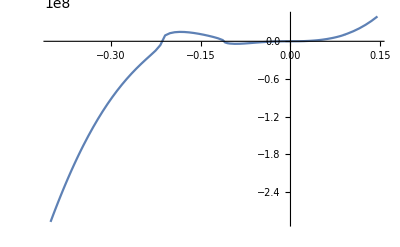

```mathematica
λ2=(x (Qpoles[mydim,spins[[2]]]/.x->x-(mydim+2-2))/.x->Rs[[2,2]])^-1 cs2^1;
ListLinePlot[Transpose[{r00,-(Sign@λ2)√Abs[λ2] r00^2}][[1;;]],PlotRange->All] (*Central Charge*)
```

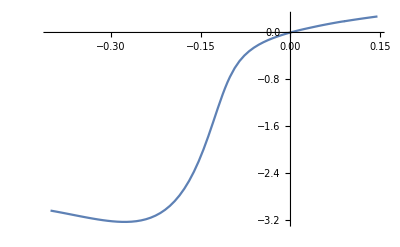

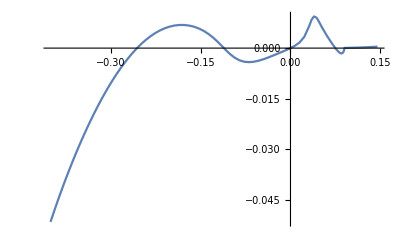

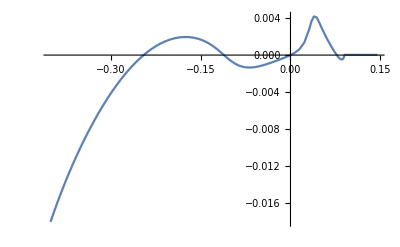

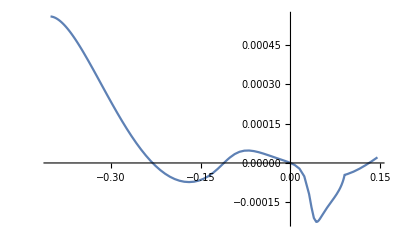

```mathematica
ListLinePlot[Transpose[{r00,-λ1}]]
ListLinePlot[Transpose[{r00,-κ1}]]
ListLinePlot[Transpose[{r00,-κ2}]]
ListLinePlot[Transpose[{r00,-κ3}]]
```

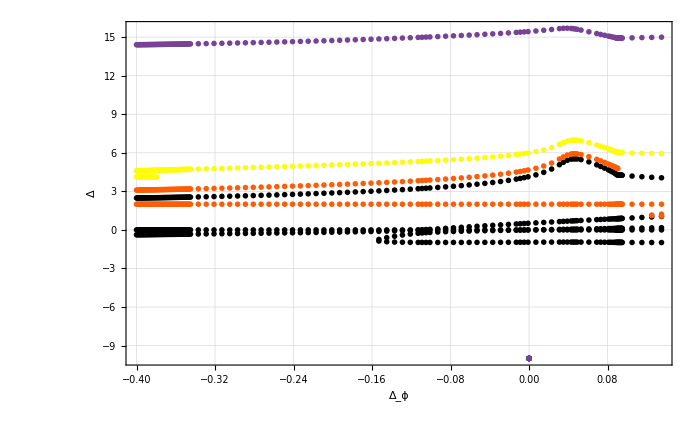

```mathematica
ppoint={{0,-10}};
Show[ListPlot[Table[ppoint~Join~Flatten[zerolist2d[1][[1;;npos]]~Join~zerolist2d[2]/.{a_,b_,c_,d_}/;b==sp∧(spins[[b]]<c+spins[[b]]<20∨b==1)∧d==double:>{a,c+spins[[b]]}/.{a_,b_,c_,d_}/;NumberQ[a]->Nothing,1]/.{}->Nothing,{sp,Length@spins}],PlotMarkers->{"⊙",Scaled[0.015]},PlotStyle->ColorData[3,"ColorList"]],
ListPlot[Table[ppoint~Join~Flatten[zerolist2d[1][[1;;npos]]~Join~zerolist2d[2]/.{a_,b_,c_,d_}/;b==sp∧(spins[[b]]+10^-1<c+spins[[b]]<20∨b==1∨b==2)∧d==single:>{a,c+spins[[b]]}/.{a_,b_,c_,d_}/;NumberQ[a]->Nothing,1]/.{}->Nothing,{sp,Length@spins}],PlotMarkers->{"●",Scaled[0.015]},PlotStyle->ColorData[3,"ColorList"]],PlotRange->{{.145,-.4},{-1,7}},ImageSize->700,Frame->True,GridLines->Automatic,FrameStyle->Thick,LabelStyle->14,FrameLabel->{"Δ_ϕ","Δ"},Axes->False]
```